```mathematica
<<xlr8r.m;
get:=Get["~/code/cellzilla/Cellzilla2D.m"];
get;
$HistoryLength=5;
```

xCellerator 0.92 (11-Nov-2012) loaded Thu 7 Mar 2013 17:40:47
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

Cellzilla2D (3.0.3 (7-March-2013)) loaded Thu 7 Mar 2013 17:40:47
using xCellerator 0.92 and XSSA 1204002
GPL License Terms Apply

## Define Tissue

```mathematica
Q=DTissue[{{-18.955967482644333,0.03491935381612028},{-18.01242969811899,-8.090465299254863},{-17.822428471437107,4.203195552384082},{-17.367128906238218,2.949748556028189},{-17.01437423674751,-0.91452895903021},{-16.849761119012737,-8.962873166868144},{-16.82263317818004,-4.816921636937595},{-16.65607731034465,-4.735372075398628},{-16.374387692841587,7.599745145785654},{-16.146445927430218,6.966237936830013},{-15.913950272322602,-4.730309461832637},{-15.064099048453526,2.506384570307015},{-14.973586808637553,-0.7286071912769944},{-14.495994422468923,-8.057270857025754},{-14.47378700100271,11.153648265501115},{-14.38878329087567,10.753691073748085},{-14.273993909289139,6.145387697863709},{-14.260752602898743,-1.1288877480808912},{-14.113073147185219,-4.055659133260253},{-13.902250891797786,3.021596017219624},{-13.171096625426966,-4.485753876746205},{-12.640038430385585,-0.465017700699026},{-12.534148722796948,-8.24883513525225},{-12.502182100369323,-8.208200307950957},{-12.484795055553707,-9.763730135060191},{-12.431670647078432,9.476149376753932},{-12.321141652564954,2.5357763011218744},{-12.244924021059227,2.565583812700191},{-12.150096287924498,6.817477833928917},{-11.715204497156183,13.904054025351513},{-11.286270329902525,13.878305734811937},{-10.9771477088575,6.217535659454543},{-10.882855590258037,-1.3187316445280752},{-10.692317850293591,-3.6408117769912627},{-10.368128013323306,6.258027955668219},{-10.170449900041001,-0.7744594408930299},{-10.169908326897145,-7.516416333980577},{-10.119823144499184,10.297273043403933},{-9.926374446048042,12.332691057696998},{-9.550442846409016,2.081429200014138},{-9.303066250019144,2.195552673599426},{-9.078230009192234,9.219310247062976},{-9.07048665271839,-4.642116810964572},{-9.020376189468376,16.476893963728024},{-8.916925142532914,5.386852839277503},{-8.257299038080653,-4.49074079244395},{-8.08233201705703,1.8407617869638955},{-7.785534853388074,-9.49712706989628},{-7.7556772122014515,-4.771526878716751},{-7.506692236802509,16.22135913059297},{-7.052456548303613,12.638334174027964},{-6.984659283519473,-1.263650044493564},{-6.9228555883535865,9.134783096117417},{-6.868919905279192,5.777617785617197},{-6.547244150812821,13.94270058356789},{-6.527560620076544,8.617819053175339},{-6.409231844328415,11.365700992932164},{-6.344767749136321,-0.7478627274976427},{-5.910652397695824,-8.501857276879463},{-5.903662843283924,4.9965315199934315},{-5.8582765739964895,-0.7254291221293221},{-5.573733077757213,3.812123902876119},{-5.495222335780573,17.93925298213042},{-5.44397304067606,-8.522838104821892},{-4.641848762910045,3.0079163306005365},{-4.3611437020271735,0.6388616823176153},{-4.204876233096195,-4.372096005921343},{-3.8695661157835985,17.44545991521985},{-3.8371018847074554,-7.770507742217115},{-3.7335199547282687,-3.615428163085263},{-3.585331612646717,11.402837972645777},{-3.582786865171608,8.571451705053125},{-3.484689370028888,-3.556615267864507},{-3.0835094191504644,9.842255074405664},{-3.061637448292946,14.224168380925093},{-2.9772076448673546,14.153138868243136},{-2.72375769262768,13.255733319282916},{-2.6735599481941104,6.834012882103417},{-2.5021251751682874,-8.083937637424851},{-2.432509770992286,6.7077224045851995},{-2.1592238587095642,-8.036222981763096},{-2.0607217873822297,0.2521579783447902},{-1.7190174735430979,3.987431087809633},{-1.5347516705610997,4.616649760051789},{-1.4137056534687362,18.92332140247167},{-1.3195496217402818,-1.6278068635576055},{-0.7811790908469605,1.887821886483652},{-0.6257593520760977,-5.391212220858964},{-0.05373642828296221,-9.149066651526141},{0.08777957905507242,15.76506883527891},{0.11181576129474922,8.061820112029965},{0.20848547091844172,11.881088026282805},{0.2163082737256766,10.183025237832243},{0.23650206927565645,10.212254423903305},{0.31995864899375187,17.636891415476992},{0.5580146777989694,-2.2688054486663134},{0.8457037939348903,-4.744504460596525},{1.0534070072592772,12.748320396352648},{1.2543964191357864,1.694830243783592},{1.2705108051013498,14.240140650733572},{1.3086094133477997,5.168588076059112},{1.625833460072804,-7.93852564128038},{1.6477931766112226,-5.2830265778552485},{1.722187618120991,6.710901134205567},{2.363218609136302,-0.791480014141962},{2.4368242367848043,3.3914275181188454},{2.6246999815106595,18.25957860558236},{3.264076829779155,7.327772414628662},{3.6175632122992276,-0.971163752094918},{3.7632632167717524,-8.792992765884376},{3.77768996302069,9.67300123522096},{3.9373411351649037,15.101177910334647},{3.9722972201624107,3.47425776031024},{3.9848270985836436,8.635475902815516},{4.016621553433613,-5.01279487048014},{4.050336332623671,-4.970786196159794},{4.203057523240279,16.99594369476444},{4.297789877696806,11.777955931081458},{4.444116391245672,11.110522803719284},{4.91687273251977,13.545395781751782},{4.995385511476325,-7.6750264819574125},{5.267863020173898,-0.3561821206849563},{5.278316621761085,4.537174660166189},{5.548561343853457,4.567461839935257},{5.821315183866587,-0.42244762869935243},{6.369257972080164,17.59750442342315},{6.637361066520591,-7.920574739103231},{6.961705621936538,5.813185998717052},{7.056086681193112,7.699813457119379},{7.255023767926056,-7.658810876550317},{7.362390052498962,13.906478990910141},{7.38832158484563,-3.8548038422280317},{7.852142031577084,8.510333920986556},{7.92614091676451,10.517063832667203},{8.169826251794683,1.202325605900357},{8.275432774742322,-4.311328350308798},{8.34190966683219,15.44973471830515},{8.43145810883017,11.12895373463602},{8.677816991041121,1.254142503209096},{9.05080198878015,-4.175675940167218},{9.327522724627718,4.848848600187683},{9.349491626921143,-8.864281929332055},{9.855360666418198,15.639619878552566},{9.856283515214276,0.7301766069090475},{10.039237698153132,-4.446740603767427},{10.30438948246833,5.336857217605984},{10.330674147838577,11.40200215246308},{10.3902322686751,7.622032464642331},{11.173387913097429,0.7644898672417979},{11.39952902231877,-3.829078444892854},{11.506643324053869,-8.096658416360043},{11.626169278619505,-8.143240267021097},{11.714299256739842,13.100113659283767},{11.813932910033634,8.65245564482268},{11.978559277409806,0.2761350520098374},{12.366248169994572,4.439481280209534},{12.46831592406879,-7.959523904972536},{12.629696455499374,8.555414765377806},{12.95763336263133,13.10097895357529},{13.776288263858877,4.941896309079986},{13.999077004989466,4.888790659886012},{14.5470285379432,-4.142375007790582},{14.795151001442461,-4.661674370132325},{14.944668140187222,10.005058063238634},{15.004273010619462,10.394953074014131},{15.26861871359461,-0.14423233087690648},{15.3402588055654,-9.374732038004169},{15.57465521664105,-0.3220334121095268},{16.41234179832483,-8.717904182332571},{16.471910264313056,-0.133414789722486},{16.51316061031023,5.676369739106054},{16.799026490450583,-5.92693095340987},{17.153133464155687,7.228910980457549},{17.189118154900832,0.4883731864440205},{18.030617971523533,-9.575744518429198},{18.207921020438036,3.1624537467523464},{-21,-12},{21,-12},{20.81278319811883,3.6730891359772886},{19.557427122295582,8.132917103191206},{17.560954171785895,12.18459253300296},{14.75317751134456,15.163861917244269},{11.170149079738232,17.715202285624443},{7.180229264994194,19.751185170682625},{3.067944271789566,20.92295413923505},{-1.5592068815486617,21.160386759252795},{-6.225863237378327,20.40710901371793},{-10.266272059660759,18.68440557649068},{-13.728775832267335,16.13706725396465},{-16.653907212132488,12.756952767075578},{-18.975038355641765,8.812026418541135},{-20.466765082532802,4.924017314477521},{-21,-0.15276954297994852},{-21,-3.9951028334855825},{-21,-8.164938049664528},{-16.432932524248695,-12},{-13.85717740039256,-12},{-9.594534623712352,-12},{-8.619701771508243,-12},{-4.5000116029398125,-12},{-2.7039636656671404,-12},{0.5210646535527484,-12},{3.7599634164847386,-12},{6.457759866412937,-12},{8.783990766548836,-12},{11.994134422683386,-12},{14.96293858330997,-12},{19.449745878371218,-12},{21,-8.952700479421525},{21,-5.036451930400661},{21,-4.005493613715901},{21,0.09068229660886094}},{{1,4},{1,5},{1,193},{2,6},{2,7},{2,195},{3,4},{3,10},{3,192},{4,12},{5,8},{5,13},{6,14},{6,196},{7,8},{7,194},{8,11},{9,10},{9,16},{9,191},{10,17},{11,14},{11,19},{12,13},{12,20},{13,18},{14,23},{15,16},{15,30},{15,190},{16,26},{17,20},{17,29},{18,19},{18,22},{19,21},{20,27},{21,24},{21,34},{22,27},{22,33},{23,24},{23,25},{24,37},{25,197},{25,198},{26,29},{26,38},{27,28},{28,32},{28,40},{29,32},{30,31},{30,189},{31,39},{31,44},{32,35},{33,34},{33,36},{34,43},{35,42},{35,45},{36,40},{36,52},{37,43},{37,48},{38,39},{38,42},{39,51},{40,41},{41,45},{41,47},{42,53},{43,46},{44,50},{44,188},{45,54},{46,49},{46,52},{47,58},{47,62},{48,59},{48,199},{49,59},{49,67},{50,55},{50,63},{51,55},{51,57},{52,58},{53,56},{53,57},{54,56},{54,60},{55,75},{56,72},{57,71},{58,61},{59,64},{60,62},{60,78},{61,66},{61,70},{62,65},{63,68},{63,187},{64,69},{64,200},{65,66},{65,83},{66,82},{67,69},{67,70},{68,75},{68,85},{69,79},{70,73},{71,74},{71,77},{72,74},{72,78},{73,86},{73,88},{74,93},{75,76},{76,77},{76,90},{77,92},{78,80},{79,81},{79,201},{80,84},{80,91},{81,88},{81,89},{82,86},{82,87},{83,84},{83,87},{84,101},{85,95},{85,186},{86,96},{87,99},{88,97},{89,102},{89,202},{90,95},{90,100},{91,93},{91,104},{92,94},{92,98},{93,94},{94,111},{95,107},{96,97},{96,105},{97,103},{98,100},{98,118},{99,105},{99,106},{100,112},{101,104},{101,106},{102,103},{102,110},{103,115},{104,108},{105,109},{106,113},{107,117},{107,185},{108,114},{108,123},{109,116},{109,122},{110,121},{110,203},{111,114},{111,119},{112,117},{112,120},{113,122},{113,123},{114,129},{115,116},{115,121},{116,132},{117,126},{118,119},{118,120},{119,134},{120,131},{121,127},{122,125},{123,124},{124,128},{124,135},{125,132},{125,135},{126,137},{126,184},{127,130},{127,204},{128,129},{128,141},{129,133},{130,136},{130,142},{131,137},{131,138},{132,136},{133,134},{133,148},{134,138},{135,139},{136,140},{137,143},{138,147},{139,141},{139,144},{140,144},{140,145},{141,146},{142,151},{142,205},{143,153},{143,183},{144,149},{145,150},{145,151},{146,148},{146,156},{147,153},{147,154},{148,154},{149,155},{149,156},{150,155},{150,162},{151,152},{152,157},{152,206},{153,159},{154,158},{155,166},{156,160},{157,163},{157,167},{158,160},{158,164},{159,165},{159,182},{160,161},{161,166},{161,171},{162,163},{162,168},{163,172},{164,165},{164,173},{165,181},{166,168},{167,169},{167,207},{168,170},{169,172},{169,175},{170,174},{170,211},{171,173},{171,176},{172,210},{173,180},{174,176},{174,212},{175,208},{175,209},{176,179},{196,197},{197,198},{178,208},{178,209},{198,199},{199,200},{200,201},{201,202},{202,203},{203,204},{204,205},{205,206},{206,207},{207,208},{209,210},{210,211},{194,195},{211,212},{187,188},{188,189},{189,190},{190,191},{191,192},{192,193},{179,212},{179,180},{180,181},{181,182},{182,183},{183,184},{184,185},{185,186},{177,195},{177,196},{186,187},{193,194}},{1->{136,143,158,162,144,137},2->{109,111,137,139,110},3->{163,162,171,178,185,172},4->{138,139,144,163,166,140},5->{132,140,165,151,133},6->{100,104,110,138,132,129,101},7->{80,98,102,109,104,81},8->{186,185,197,202,200,198},9->{165,166,172,186,176,170},10->{71,72,81,100,94,77},11->{63,64,90,80,72,70},12->{200,218,222,208,199},13->{176,198,199,207,187,175},14->{150,151,170,175,181,155,154},15->{120,121,129,133,150,124},16->{94,101,121,96,93},17->{92,91,96,120,118,97},18->{62,77,93,91,73,61},19->{50,51,70,71,62,57},20->{40,41,59,63,51,49},21->{222,223,231,240,235,226},22->{207,208,226,234,216,209},23->{181,187,209,215,194,182},24->{152,155,182,192,161,153},25->{118,124,154,152,128,119},26->{32,37,49,50,52,33},27->{24,26,35,40,37,25},28->{240,239,248,257,256,249},29->{234,235,249,252,247,238},30->{217,215,216,238,237,221},31->{193,192,194,217,213,195},32->{160,161,193,184,164},33->{126,128,153,160,149,127},34->{88,89,97,119,126,125,95},35->{67,68,73,92,89,69},36->{47,52,57,61,68,48},37->{28,31,48,67,55,53,29},38->{18,21,33,47,31,19},39->{7,10,25,32,21,8},40->{2,12,24,10,1},41->{257,265,268,271,277,274,258},42->{252,256,258,273,263,253},43->{236,237,247,253,262,254,246},44->{212,213,221,236,229,220},45->{183,184,195,212,203,191},46->{148,149,164,183,173,156},47->{114,125,127,148,141,115},48->{86,95,114,105,87},49->{55,69,88,86,75,56},50->{75,87,106,300,76},51->{53,56,76,301,54},52->{29,54,302,30},53->{19,28,30,303,20},54->{8,18,20,304,9},55->{1,7,9,305,3},56->{277,281,306,278},57->{273,276,307,281,274},58->{262,264,308,276,263},59->{254,264,309,255},60->{229,246,255,310,230},61->{203,220,230,311,204},62->{173,191,204,312,174},63->{141,156,174,313,142},64->{105,115,142,316,106},65->{315,14,4,6,314},66->{5,4,13,22,17,15},67->{2,11,15,16,317,3},68->{13,27,43,45,282,14},69->{22,27,42,38,36,23},70->{11,17,23,34,26,12},71->{45,283,46},72->{38,44,65,60,39},73->{34,36,39,58,41,35},74->{42,44,66,83,286,46,43},75->{65,66,82,84,78,74},76->{59,58,60,74,79,64},77->{82,99,108,287,83},78->{84,99,107,112,85},79->{90,79,78,85,113,103,98},80->{107,116,131,288,108},81->{113,112,116,130,134,123,117},82->{103,117,122,136,111,102},83->{130,135,147,289,131},84->{134,135,146,167,159,145},85->{123,145,157,143,122},86->{146,168,180,290,147},87->{167,168,179,189,169},88->{157,159,169,188,177,171,158},89->{179,196,206,291,180},90->{188,189,196,205,210,214,190},91->{177,190,201,197,178},92->{205,211,228,292,206},93->{210,211,227,233,225,219},94->{202,201,214,219,224,223,218},95->{227,243,245,293,228},96->{232,233,243,244,250,259,242},97->{224,225,232,241,239,231},98->{244,251,267,294,245},99->{251,266,269,261,250},100->{242,260,265,248,241},101->{266,270,279,295,267},102->{269,275,296,280,270},103->{259,261,275,297,272,268,260},104->{285,280,279,284},105->{5,16,298,6},106->{271,278,299,272}}];
```

## Define Initial Conditions

```mathematica
myic={S[1]->1,S[2]->1,S[3]->1,S[4]->0,S[5]->0,S[6]->0,S[7]->1,S[8]->1,S[9]->0,S[10]->0,S[11]->1,S[12]->1,S[13]->0,S[14]->0,S[15]->0,S[16]->0,S[17]->0,S[18]->0,S[19]->0,S[20]->1,S[21]->1,S[22]->0,S[23]->0,S[24]->0,S[25]->0,S[26]->0,S[27]->1,S[28]->1,S[29]->0,S[30]->0,S[31]->0,S[32]->0,S[33]->0,S[34]->0,S[35]->0,S[36]->0,S[37]->0,S[38]->0,S[39]->0,S[40]->1,S[41]->1,S[42]->0,S[43]->0,S[44]->0,S[45]->0,S[46]->0,S[47]->0,S[48]->0,S[49]->0,S[50]->0,S[51]->0,S[52]->0,S[53]->0,S[54]->0,S[55]->1,S[56]->1,S[57]->0,S[58]->0,S[59]->0,S[60]->0,S[61]->0,S[62]->0,S[63]->0,S[64]->0,S[65]->1,S[66]->1,S[67]->1,S[68]->1,S[69]->1,S[70]->1,S[71]->1,S[72]->1,S[73]->1,S[74]->1,S[75]->1,S[76]->1,S[77]->1,S[78]->1,S[79]->1,S[80]->1,S[81]->1,S[82]->1,S[83]->1,S[84]->1,S[85]->1,S[86]->1,S[87]->1,S[88]->1,S[89]->1,S[90]->1,S[91]->1,S[92]->1,S[93]->1,S[94]->1,S[95]->1,S[96]->1,S[97]->1,S[98]->1,S[99]->1,S[100]->1,S[101]->1,S[102]->1,S[103]->1,S[104]->1,S[105]->1,S[106]->1,PZ[1]->0,PZ[2]->0,PZ[3]->0,PZ[4]->0,PZ[5]->0,PZ[6]->0,PZ[7]->0,PZ[8]->0,PZ[9]->0,PZ[10]->0,PZ[11]->0,PZ[12]->0,PZ[13]->0,PZ[14]->0,PZ[15]->0,PZ[16]->0,PZ[17]->0,PZ[18]->0,PZ[19]->0,PZ[20]->0,PZ[21]->0,PZ[22]->0,PZ[23]->0,PZ[24]->0,PZ[25]->0,PZ[26]->0,PZ[27]->0,PZ[28]->0,PZ[29]->0,PZ[30]->0,PZ[31]->0,PZ[32]->0,PZ[33]->0,PZ[34]->0,PZ[35]->0,PZ[36]->0,PZ[37]->0,PZ[38]->0,PZ[39]->0,PZ[40]->0,PZ[41]->0,PZ[42]->0,PZ[43]->0,PZ[44]->0,PZ[45]->0,PZ[46]->0,PZ[47]->0,PZ[48]->0,PZ[49]->0,PZ[50]->0,PZ[51]->1,PZ[52]->1,PZ[53]->1,PZ[54]->1,PZ[55]->1,PZ[56]->1,PZ[57]->1,PZ[58]->1,PZ[59]->1,PZ[60]->1,PZ[61]->1,PZ[62]->0,PZ[63]->0,PZ[64]->0,PZ[65]->0,PZ[66]->0,PZ[67]->0,PZ[68]->0,PZ[69]->0,PZ[70]->0,PZ[71]->0,PZ[72]->0,PZ[73]->0,PZ[74]->0,PZ[75]->0,PZ[76]->0,PZ[77]->0,PZ[78]->0,PZ[79]->0,PZ[80]->0,PZ[81]->0,PZ[82]->0,PZ[83]->0,PZ[84]->0,PZ[85]->0,PZ[86]->0,PZ[87]->0,PZ[88]->0,PZ[89]->0,PZ[90]->0,PZ[91]->0,PZ[92]->0,PZ[93]->0,PZ[94]->0,PZ[95]->0,PZ[96]->0,PZ[97]->0,PZ[98]->0,PZ[99]->0,PZ[100]->0,PZ[101]->0,PZ[102]->0,PZ[103]->0,PZ[104]->0,PZ[105]->0,PZ[106]->0,W[1]->0,W[2]->0,W[3]->0,W[4]->0,W[5]->0,W[6]->0,W[7]->0,W[8]->0,W[9]->0,W[10]->0,W[11]->0,W[12]->0,W[13]->0,W[14]->0,W[15]->0,W[16]->0,W[17]->0,W[18]->0,W[19]->0,W[20]->0,W[21]->0,W[22]->0,W[23]->0,W[24]->1,W[25]->1,W[26]->0,W[27]->0,W[28]->0,W[29]->0,W[30]->0,W[31]->0,W[32]->1,W[33]->1,W[34]->0,W[35]->0,W[36]->0,W[37]->0,W[38]->0,W[39]->0,W[40]->0,W[41]->0,W[42]->0,W[43]->0,W[44]->0,W[45]->0,W[46]->0,W[47]->0,W[48]->0,W[49]->0,W[50]->0,W[51]->0,W[52]->0,W[53]->0,W[54]->0,W[55]->0,W[56]->0,W[57]->0,W[58]->0,W[59]->0,W[60]->0,W[61]->0,W[62]->0,W[63]->0,W[64]->0,W[65]->0,W[66]->0,W[67]->0,W[68]->0,W[69]->0,W[70]->0,W[71]->0,W[72]->0,W[73]->0,W[74]->0,W[75]->0,W[76]->0,W[77]->0,W[78]->0,W[79]->0,W[80]->0,W[81]->0,W[82]->0,W[83]->0,W[84]->0,W[85]->0,W[86]->0,W[87]->0,W[88]->0,W[89]->0,W[90]->0,W[91]->0,W[92]->0,W[93]->0,W[94]->0,W[95]->0,W[96]->0,W[97]->0,W[98]->0,W[99]->0,W[100]->0,W[101]->0,W[102]->0,W[103]->0,W[104]->0,W[105]->0,W[106]->0,Tip[1]->0,Tip[2]->0,Tip[3]->0,Tip[4]->0,Tip[5]->0,Tip[6]->0,Tip[7]->0,Tip[8]->0,Tip[9]->0,Tip[10]->0,Tip[11]->0,Tip[12]->0,Tip[13]->0,Tip[14]->0,Tip[15]->0,Tip[16]->0,Tip[17]->0,Tip[18]->0,Tip[19]->0,Tip[20]->0,Tip[21]->0,Tip[22]->0,Tip[23]->0,Tip[24]->0,Tip[25]->0,Tip[26]->0,Tip[27]->0,Tip[28]->0,Tip[29]->0,Tip[30]->0,Tip[31]->0,Tip[32]->0,Tip[33]->0,Tip[34]->0,Tip[35]->0,Tip[36]->0,Tip[37]->0,Tip[38]->0,Tip[39]->0,Tip[40]->0,Tip[41]->0,Tip[42]->0,Tip[43]->0,Tip[44]->0,Tip[45]->0,Tip[46]->0,Tip[47]->0,Tip[48]->0,Tip[49]->0,Tip[50]->1,Tip[51]->0,Tip[52]->0,Tip[53]->0,Tip[54]->0,Tip[55]->0,Tip[56]->0,Tip[57]->0,Tip[58]->0,Tip[59]->0,Tip[60]->0,Tip[61]->0,Tip[62]->1,Tip[63]->1,Tip[64]->1,Tip[65]->0,Tip[66]->0,Tip[67]->0,Tip[68]->0,Tip[69]->0,Tip[70]->0,Tip[71]->0,Tip[72]->0,Tip[73]->0,Tip[74]->0,Tip[75]->0,Tip[76]->0,Tip[77]->0,Tip[78]->0,Tip[79]->0,Tip[80]->0,Tip[81]->0,Tip[82]->0,Tip[83]->0,Tip[84]->0,Tip[85]->0,Tip[86]->0,Tip[87]->0,Tip[88]->0,Tip[89]->0,Tip[90]->0,Tip[91]->0,Tip[92]->0,Tip[93]->0,Tip[94]->0,Tip[95]->0,Tip[96]->0,Tip[97]->0,Tip[98]->0,Tip[99]->0,Tip[100]->0,Tip[101]->0,Tip[102]->0,Tip[103]->0,Tip[104]->0,Tip[105]->0,Tip[106]->0,U[1]->0,U[2]->0,U[3]->0,U[4]->0,U[5]->0,U[6]->0,U[7]->0,U[8]->0,U[9]->0,U[10]->0,U[11]->0,U[12]->0,U[13]->0,U[14]->0,U[15]->0,U[16]->0,U[17]->0,U[18]->0,U[19]->0,U[20]->0,U[21]->0,U[22]->0,U[23]->0,U[24]->0,U[25]->0,U[26]->0,U[27]->0,U[28]->0,U[29]->0,U[30]->0,U[31]->0,U[32]->0,U[33]->0,U[34]->0,U[35]->0,U[36]->0,U[37]->0,U[38]->0,U[39]->0,U[40]->0,U[41]->0,U[42]->0,U[43]->0,U[44]->0,U[45]->0,U[46]->0,U[47]->0,U[48]->0,U[49]->0,U[50]->0,U[51]->0,U[52]->0,U[53]->0,U[54]->0,U[55]->0,U[56]->0,U[57]->0,U[58]->0,U[59]->0,U[60]->0,U[61]->0,U[62]->0,U[63]->0,U[64]->0,U[65]->0,U[66]->0,U[67]->0,U[68]->0,U[69]->0,U[70]->0,U[71]->0,U[72]->0,U[73]->0,U[74]->0,U[75]->0,U[76]->0,U[77]->0,U[78]->0,U[79]->0,U[80]->0,U[81]->0,U[82]->0,U[83]->0,U[84]->0,U[85]->0,U[86]->0,U[87]->0,U[88]->0,U[89]->0,U[90]->0,U[91]->0,U[92]->0,U[93]->0,U[94]->0,U[95]->0,U[96]->0,U[97]->0,U[98]->0,U[99]->0,U[100]->0,U[101]->0,U[102]->0,U[103]->0,U[104]->0,U[105]->0,U[106]->0,X[1]->0,X[2]->0,X[3]->0,X[4]->0,X[5]->0,X[6]->0,X[7]->0,X[8]->0,X[9]->0,X[10]->0,X[11]->0,X[12]->0,X[13]->0,X[14]->0,X[15]->0,X[16]->0,X[17]->0,X[18]->0,X[19]->0,X[20]->0,X[21]->0,X[22]->0,X[23]->0,X[24]->0,X[25]->0,X[26]->0,X[27]->0,X[28]->0,X[29]->0,X[30]->0,X[31]->0,X[32]->0,X[33]->0,X[34]->0,X[35]->0,X[36]->0,X[37]->0,X[38]->0,X[39]->0,X[40]->0,X[41]->0,X[42]->0,X[43]->0,X[44]->0,X[45]->0,X[46]->0,X[47]->0,X[48]->0,X[49]->0,X[50]->0,X[51]->0,X[52]->0,X[53]->0,X[54]->0,X[55]->0,X[56]->0,X[57]->0,X[58]->0,X[59]->0,X[60]->0,X[61]->0,X[62]->0,X[63]->0,X[64]->0,X[65]->0,X[66]->0,X[67]->0,X[68]->0,X[69]->0,X[70]->0,X[71]->0,X[72]->0,X[73]->0,X[74]->0,X[75]->0,X[76]->0,X[77]->0,X[78]->0,X[79]->0,X[80]->0,X[81]->0,X[82]->0,X[83]->0,X[84]->0,X[85]->0,X[86]->0,X[87]->0,X[88]->0,X[89]->0,X[90]->0,X[91]->0,X[92]->0,X[93]->0,X[94]->0,X[95]->0,X[96]->0,X[97]->0,X[98]->0,X[99]->0,X[100]->0,X[101]->0,X[102]->0,X[103]->0,X[104]->0,X[105]->0,X[106]->0,Z[1]->0,Z[2]->0,Z[3]->0,Z[4]->0,Z[5]->0,Z[6]->0,Z[7]->0,Z[8]->0,Z[9]->0,Z[10]->0,Z[11]->0,Z[12]->0,Z[13]->0,Z[14]->0,Z[15]->0,Z[16]->0,Z[17]->0,Z[18]->0,Z[19]->0,Z[20]->0,Z[21]->0,Z[22]->0,Z[23]->0,Z[24]->0,Z[25]->0,Z[26]->0,Z[27]->0,Z[28]->0,Z[29]->0,Z[30]->0,Z[31]->0,Z[32]->0,Z[33]->0,Z[34]->0,Z[35]->0,Z[36]->0,Z[37]->0,Z[38]->0,Z[39]->0,Z[40]->0,Z[41]->0,Z[42]->0,Z[43]->0,Z[44]->0,Z[45]->0,Z[46]->0,Z[47]->0,Z[48]->0,Z[49]->0,Z[50]->0,Z[51]->0,Z[52]->0,Z[53]->0,Z[54]->0,Z[55]->0,Z[56]->0,Z[57]->0,Z[58]->0,Z[59]->0,Z[60]->0,Z[61]->0,Z[62]->0,Z[63]->0,Z[64]->0,Z[65]->0,Z[66]->0,Z[67]->0,Z[68]->0,Z[69]->0,Z[70]->0,Z[71]->0,Z[72]->0,Z[73]->0,Z[74]->0,Z[75]->0,Z[76]->0,Z[77]->0,Z[78]->0,Z[79]->0,Z[80]->0,Z[81]->0,Z[82]->0,Z[83]->0,Z[84]->0,Z[85]->0,Z[86]->0,Z[87]->0,Z[88]->0,Z[89]->0,Z[90]->0,Z[91]->0,Z[92]->0,Z[93]->0,Z[94]->0,Z[95]->0,Z[96]->0,Z[97]->0,Z[98]->0,Z[99]->0,Z[100]->0,Z[101]->0,Z[102]->0,Z[103]->0,Z[104]->0,Z[105]->0,Z[106]->0,Y[1]->0,Y[2]->0,Y[3]->0,Y[4]->0,Y[5]->0,Y[6]->0,Y[7]->0,Y[8]->0,Y[9]->0,Y[10]->0,Y[11]->0,Y[12]->0,Y[13]->0,Y[14]->0,Y[15]->0,Y[16]->0,Y[17]->0,Y[18]->0,Y[19]->0,Y[20]->0,Y[21]->0,Y[22]->0,Y[23]->0,Y[24]->0,Y[25]->0,Y[26]->0,Y[27]->0,Y[28]->0,Y[29]->0,Y[30]->0,Y[31]->0,Y[32]->0,Y[33]->0,Y[34]->0,Y[35]->0,Y[36]->0,Y[37]->0,Y[38]->0,Y[39]->0,Y[40]->0,Y[41]->0,Y[42]->0,Y[43]->0,Y[44]->0,Y[45]->0,Y[46]->0,Y[47]->0,Y[48]->0,Y[49]->0,Y[50]->0,Y[51]->0,Y[52]->0,Y[53]->0,Y[54]->0,Y[55]->0,Y[56]->0,Y[57]->0,Y[58]->0,Y[59]->0,Y[60]->0,Y[61]->0,Y[62]->0,Y[63]->0,Y[64]->0,Y[65]->0,Y[66]->0,Y[67]->0,Y[68]->0,Y[69]->0,Y[70]->0,Y[71]->0,Y[72]->0,Y[73]->0,Y[74]->0,Y[75]->0,Y[76]->0,Y[77]->0,Y[78]->0,Y[79]->0,Y[80]->0,Y[81]->0,Y[82]->0,Y[83]->0,Y[84]->0,Y[85]->0,Y[86]->0,Y[87]->0,Y[88]->0,Y[89]->0,Y[90]->0,Y[91]->0,Y[92]->0,Y[93]->0,Y[94]->0,Y[95]->0,Y[96]->0,Y[97]->0,Y[98]->0,Y[99]->0,Y[100]->0,Y[101]->0,Y[102]->0,Y[103]->0,Y[104]->0,Y[105]->0,Y[106]->0};
```

## Setup Internal Simulation

```mathematica
w=DTissue2Tissue[Q];
```

```mathematica
net={
(* Self Activation of S *)
{X↦S, GRN[vS,TXS,1,hS,sigma]}, 
{S->S+X,kXf}, {X->∅,kXr}, {S->∅,kSr},
{Y↦S, GRN[vS,TYS,1,hS,sigma]}, 
{Z↦S, GRN[vS,TZS,1,hS,sigma]}, 
{U↦S, GRN[vS,TUS,1,hS,sigma]}, 

(* Self Activation / mutual inhibition of Tip *)
{U↦Tip, GRN[vTip,TUTip,1,hT,sigma]}, 
{Tip->Tip+U,kUf}, {U->∅,kUr}, {Tip->∅,kTipr},
{X↦Tip, GRN[vL,TXTip,1,hT,sigma]}, 
{Y↦Tip, GRN[vL,TYTip,1,hT,sigma]},
{Z↦Tip, GRN[vL,TZTip,1,hT,sigma]},


(* Self Activation / mutual inhibition of PZ *)
{Z↦PZ, GRN[vP,TZP,1,hP,sigma]}, 
{PZ->PZ+Z,kZf}, {Z->∅,kZr}, {PZ->∅,kPr},
{X↦PZ, GRN[vP,TXP,1,hP,sigma]}, 
{Y↦PZ, GRN[vP,TYP,1,hP,sigma]}, 
{U↦PZ, GRN[vP,TUP,1,hP,sigma]}, 

(* Self Activation / mutual inhibition of W *)
{Y↦W, GRN[vW,TYW,1,hW,sigma]}, 
{W->W+Y,kYf}, {Y->∅,kYr}, {W->∅,kWr},
{X↦W, GRN[vW,TXW,1,hW,sigma]}, 
{Z↦W, GRN[vW,TZW,1,hW,sigma]},
{U↦W, GRN[vW,TUW,1,hW,sigma]}

};
```

```mathematica
{cpu,bignet}=Timing[CelleratorNetwork[w,"Reactions"-> net,
"Diffusion"->{{X,DX}, {Y,DY}, {Z, DZ}, {U, DU}}] ];
Print[cpu," seconds to generate network"]
```

106 Cells.

28 internal reactions in each cell.

2968 intracellular reactions.

2248 diffusion reactions.

5216 total reactions.

0.300019 seconds to generate network

```mathematica
{cpu,istn}=Timing[interpret[bignet]];Print[cpu, " seconds to interpret network"];
```

2.34015 seconds to interpret network

```mathematica
parameters= {kXf-> 1, kXr-> 1,kZf-> 1, kZr-> 1,kYf-> 1, kYr-> 1, kUf->1, kUr-> 1, 
kSr-> 1,kPr-> 1,kWr-> 1,  kTipr-> 1, 
TXS-> 10,TYS-> -15, TZS-> -15, TUS-> -15, 
TZP-> 10, TXP-> -10, TYP-> -10, TUP-> -10, 
TYW-> 10,TXW-> -22, TZW-> -10, TUW -> -10, 
TUTip-> 10, TXTip-> -10, TYTip-> -22, TZTip-> -10, 
hS-> 0,hP-> 0, hW-> 0, hT-> 0, 
DX-> 1, DY-> 1, DZ-> 1, DU-> 1,
vW-> 1, vS-> 1, vTip-> 1, vP-> 1
};
```

```mathematica
sim=run[istn/.parameters,{0,300},initialConditions->myic];
```

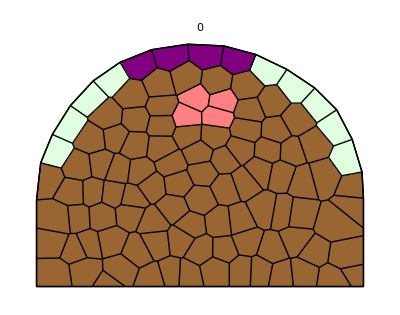
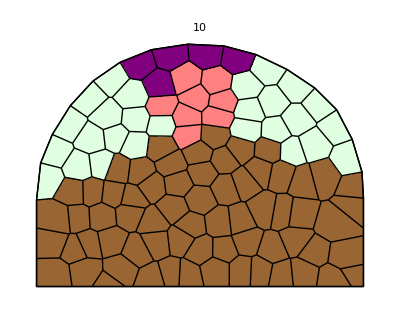
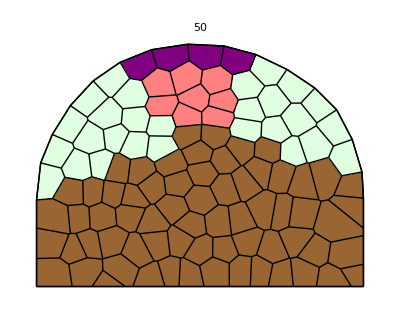
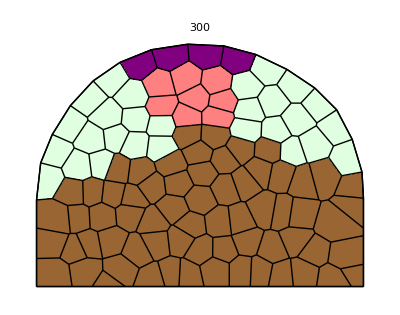

```mathematica
WTAShow[w,sim,#,{W, Tip,PZ, S}, {Pink, Purple, LightGreen, Brown}, PlotLabel-> #]&/@{0,10,50,300}
```